# Classifying cellular automata with machine learning

## Karan Shah Wolfram Summer School 2016

Introduction
As we have seen for k = 2, r = 1 cellular automata (Elementary cellular automata), there exist certain classification systems for cellular automata based on how they behave over time [1]. These were obtained by individually studying each rule and manually determining classes. 

-Graphics-Image reference[1]

There are other classification systems like Kurka’s classification and Li Packard classification which depend on the the behavior of the rules [2]. The number of total possible rules is given by the following formula: k^(k^((2r+1)^d)), 
where k is the number of colors, r is the range and d is the number of dimensions [3]. The following object calculates the number of rules with
these parameters :

```mathematica
Manipulate[N[k^k^(2*r+1)^d],{{k,2},1,10,1},{r,1,5,1},{d,1,2,1}]
```

Proposal
l plan on using unsupervised learning techniques to find group cellular automata that are similar to each other based on certain properties. This allows to quickly classify large samples of cellular automata without going through the entire space. The classifier and clustering functions in Wolfram Language can be used to do so. The main problem is figuring out what features to select and what representation of the cellular automata input is the most optimal for classifications. Some examples of features include the ratios of different colored cells, the central column, boundary shape and repeating patterns. These can be used to quantize the behavior of these cellular automata. The representation of cellular automata might also affect classification. Representations include array plot images, bit vectors and boolean formula [4] (other properties can be found in [4]). By experimenting with these parameters, l can find the best way to classify
cellular automata without looking at each of them individually. That is the goal of my project.

Apart from this, l can also use supervised learning and train the algorithm with some samples that l classified manually and let it classify a very large sample.

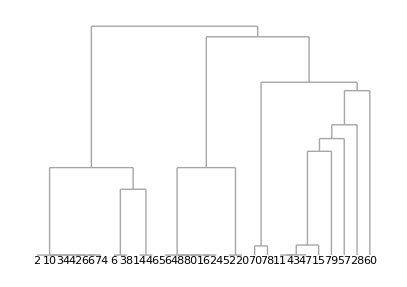
Figures and preliminary results
Some results from running the classifier without any optimization (used auto classification criteria and arrayplot images as input):

1D 2 color Automata:
Some visually similar cellular automata were in the same cluster:
-Graphics-
Above: Alternating diagonals with alternating background


-Graphics-
Above: Some Sierpinski triangles

Some clusters had seemingly unrelated members:
-Graphics-


A dendogram with some rules classified. This was created using the dendogram function and with flattened bit vectors as input (Mouse over the number to see the plot) [5]:
-Graphics-

2D 3 Color Totalistic Automata:
On applying it to a small sample of 10 rules, it did not classify them:
-Graphics-

References

[1] Wolfram, S., A New Kind of Science p231, (Wolfram Media, Champaign, IL, 2002).

[2] Sutner, K., Classification of Cellular Automata. http://www.cs.cmu.edu/~sutner/papers/ecss.pdf

[3] Anon., CellularAutomaton Reference, http://reference.wolfram.com/language/ref/CellularAutomaton.html#7022

[4] Wolfram, S.,  Tables of Cellular Automaton Properties (n.d.). http://www.stephenwolfram.com/publications/academic/cellular-automaton-properties.pdf

[5] Dendrogram code by my mentor Giorgia Fortuna